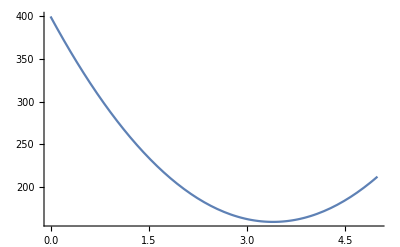

```mathematica
Plot[31.25 t^2+(-10.4 t^2-141.9t)+400,{t,0,5}]
```

```mathematica
31.25(3.4)^2+(-10.4(3.4)^2-141.9(3.4))+400
```

158.566

Set::write: Tag C in C[t] is Protected.

72.9+41.7 t+14 cos (-(2 pi)/3+(2 pi t)/365)

```mathematica
31.25 t^2+(-10.4 t^2+141.9t)//FullSimplify
```

t (141.9+20.85 t)

```mathematica
Plot3D[31.25 t^2+(-10.4 t^2-141.9t)+(T-83.4)^2/50+400,{t,0,5},{T,40,100}]
```

-Graphics3D-

```mathematica
F[t_,T_]:=31.25 t^2+(-10.4 t^2-141.9t)+(T-83.4)^2/50+400
```

```mathematica
Solve[D[F[t,T],t]==0]
```

{{t→3.40288}}

```mathematica
Solve[D[F[t,T],T]==0]
```

{{T→83.4}}

## Pt 2

change in oil
change inbacteria

```mathematica
fO[b_,O_]=1000-5b
fb[b_,O_]=5O-(b-100)
```

1000-5 b

100-b+5 O

```mathematica
Solve[{1000-5b==0,5O-(b-100)==0},{b,O}]
```

{{b→200,O→20}}

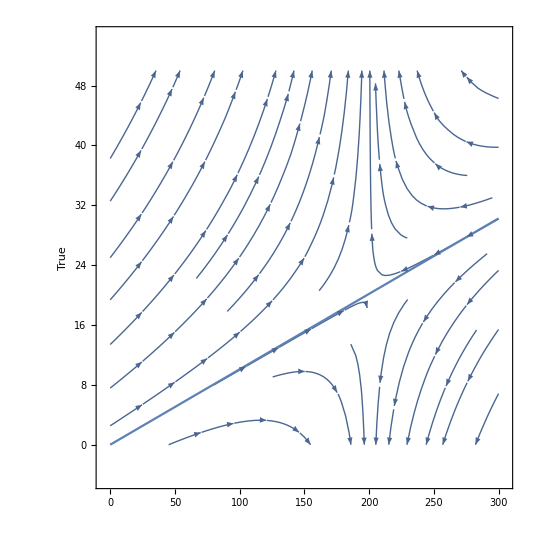

```mathematica
Show[StreamPlot[{fO[b,O],fb[b,O]},{b,0,300},{O,0,50},Frame->True, AxesLabel->True],Plot[y=.10082x ,{x,0,300}]]
```

```mathematica
Det[({{0-λ, -5}, {-1, 5-λ}})]
```

-5-5 λ+λ^2

```mathematica
Solve[-5-5 λ+λ^2==0,λ]//N
```

{{λ→-0.854102},{λ→5.8541}}

```mathematica
({{-1/2 (5-3 √5), -5}, {-1, 5-1/2 (5-3 √5)}})({{x}, {y}})=({{0}, {0}})
```

```mathematica
Solve[{(-1/2 (5-3 √5))*x-5y2==0&&-x+(5-1/2 (5-3 √5))y2==0},{x,y2}]//N
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y2→0.17082 x}}

```mathematica
({{-1/2 (5+3 √5), -5}, {-1, 5-1/2 (5+3 √5)}})({{x}, {y}})=({{0}, {0}})
```

Set::write: Tag Times in {{x}, {30.1344}}\ {{1/2\ (-5 - 3\ √5), -5}, {-1, 5 + 1/2\ (-5 - 3\ Power[« 2 »])}} is Protected.

{{0},{0}}

```mathematica
Solve[{(-1/2 (5+3 √5))*x1-5y1==0&&-x1+(5-1/2 (5+3 √5))y1==0},{x1,y1}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y1→-1/10 (5+3 √5) x1}}

Sensitivity on optimum growth temp for bacteria

```mathematica
F[g_]:=31.25(3.4)^2+(-10.4(3.4)^2-141.9*3.4)+(83.4-g)^2/50+400//N
```

```mathematica
F[g]
```

158.566+1/50 (83.4-g)^2

```mathematica
Solve[D[F[t,T],t]==0]
```

{{t→3.40288}}

```mathematica
Solve[D[F[t,T],T]==0]
```

{{T→g}}

```mathematica
Solve[D[F[t,T],T]==0,T]//Simplify
```

{{T→g}}

```mathematica
f[g_]=g
```

g

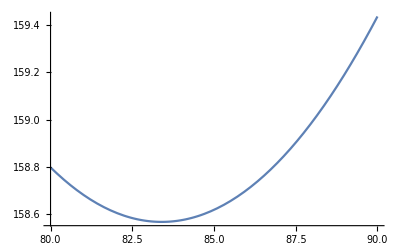

```mathematica
Plot[F[g], {g,80,90}]
```

```mathematica
Plot
```

Plot

```mathematica
Eigenvalues[({{0, -5}, {-1, 5}})]
```

{1/2 (5+3 √5),1/2 (5-3 √5)}

```mathematica
Eigenvectors[({{0, -5}, {-1, 5}})]//N
```

{{-0.854102,1.},{5.8541,1.}}

```mathematica
c[cg_]:=cg*(3.4)^2+(-10.4(3.4)-141.9)*(3.4)+400
```

```mathematica
c[cg]
```

-202.684+11.56 cg

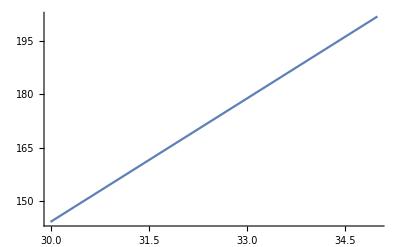

```mathematica
Plot[c[cg], {cg,30,35}]
```

```mathematica
3.4*3.4
```

11.56